## G_2

```mathematica
Remove["Global`*"]
```

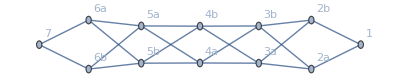

20

```mathematica
G=UndirectedGraph[{
"1"->"2a","2a"->"3a","3a"->"4a","4a"->"5a","5a"->"6a","6a"->"7",
"1"->"2b","2b"->"3b","3b"->"4b","4b"->"5b","5b"->"6b","6b"->"7",
"2a"->"3b","3a"->"4b","4a"->"5b","5a"->"6b",
"2b"->"3a","3b"->"4a","4b"->"5a","5b"->"6a"},
VertexLabels->"Name"]
nEdges = EdgeCount[G]
```

```mathematica
CycleAllowedQ[c_]:=Length[DeleteDuplicates[First/@Characters/@DeleteDuplicates[Flatten[Table[ToString[c[[j,k]]],{j,1,4},{k,1,2}]]]]]==3
cycles = Select[FindCycle[G,{4},All],CycleAllowedQ]
Length[cycles]
```

{{6a<->5b,5b<->6b,6b<->7,7<->6a},{5a<->6a,6a<->5b,5b<->4b,4b<->5a},{5a<->4b,4b<->5b,5b<->6b,6b<->5a},{5a<->6a,6a<->7,7<->6b,6b<->5a},{4a<->5a,5a<->4b,4b<->3b,3b<->4a},{4a<->3b,3b<->4b,4b<->5b,5b<->4a},{4a<->5a,5a<->6a,6a<->5b,5b<->4a},{4a<->5a,5a<->6b,6b<->5b,5b<->4a},{3a<->4a,4a<->3b,3b<->2b,2b<->3a},{3a<->2b,2b<->3b,3b<->4b,4b<->3a},{3a<->4a,4a<->5a,5a<->4b,4b<->3a},{3a<->4a,4a<->5b,5b<->4b,4b<->3a},{2a<->3b,3b<->4b,4b<->3a,3a<->2a},{2a<->3b,3b<->4a,4a<->3a,3a<->2a},{1<->2a,2a<->3a,3a<->2b,2b<->1},{1<->2a,2a<->3b,3b<->2b,2b<->1}}

16

```mathematica
NormalFormEdge[e_]:=UndirectedEdge@@Sort[{e[[1]],e[[2]]}]
edgeAssoc = Association[#[[1]]->#[[2]]&/@Transpose[{NormalFormEdge/@EdgeList[G],Range[nEdges]}]]
edgeAssocInverse = Association[#[[1]]->#[[2]]&/@Transpose[{Range[nEdges],NormalFormEdge/@EdgeList[G]}]]
```

<|1<->2a→1,1<->2b→2,2a<->3a→3,2a<->3b→4,2b<->3a→5,3a<->4a→6,3a<->4b→7,3b<->4a→8,4a<->5a→9,4a<->5b→10,4b<->5a→11,5a<->6a→12,5a<->6b→13,5b<->6a→14,6a<->7→15,6b<->7→16,2b<->3b→17,3b<->4b→18,4b<->5b→19,5b<->6b→20|>

<|1→1<->2a,2→1<->2b,3→2a<->3a,4→2a<->3b,5→2b<->3a,6→3a<->4a,7→3a<->4b,8→3b<->4a,9→4a<->5a,10→4a<->5b,11→4b<->5a,12→5a<->6a,13→5a<->6b,14→5b<->6a,15→6a<->7,16→6b<->7,17→2b<->3b,18→3b<->4b,19→4b<->5b,20→5b<->6b|>

```mathematica
cycleNumbers=Sort/@Map[edgeAssoc@*NormalFormEdge,cycles,{2}]
```

{{14,15,16,20},{11,12,14,19},{11,13,19,20},{12,13,15,16},{8,9,11,18},{8,10,18,19},{9,10,12,14},{9,10,13,20},{5,6,8,17},{5,7,17,18},{6,7,9,11},{6,7,10,19},{3,4,7,18},{3,4,6,8},{1,2,3,5},{1,2,4,17}}

```mathematica
BadCycles[signs_]:=Position[Times@@signs[[#]]&/@cycleNumbers,1]//Flatten
```

```mathematica
BadEdges[cycles_]:=cycleNumbers[[cycles]]//Flatten//DeleteDuplicates
```

```mathematica
signs=RandomChoice[{-1,1},nEdges];
badCycles = BadCycles[signs];
While[Length[badCycles]>0,
choice= RandomChoice[BadEdges[badCycles]];
signs[[choice]]=-1*signs[[choice]];
badCycles=BadCycles[signs];
]
signs
Total[signs]
```

{-1,-1,1,-1,-1,-1,1,-1,-1,-1,-1,-1,-1,1,1,-1,1,1,-1,1}

-6

```mathematica
eLabels = #[[1]]->#[[2]]&/@({edgeAssocInverse/@Range[nEdges],<|1->Blue,-1->Red|>/@signs}//Transpose)
```

{1<->2a→RGBColor[1, 0, 0],1<->2b→RGBColor[1, 0, 0],2a<->3a→RGBColor[0, 0, 1],2a<->3b→RGBColor[1, 0, 0],2b<->3a→RGBColor[1, 0, 0],3a<->4a→RGBColor[1, 0, 0],3a<->4b→RGBColor[0, 0, 1],3b<->4a→RGBColor[1, 0, 0],4a<->5a→RGBColor[1, 0, 0],4a<->5b→RGBColor[1, 0, 0],4b<->5a→RGBColor[1, 0, 0],5a<->6a→RGBColor[1, 0, 0],5a<->6b→RGBColor[1, 0, 0],5b<->6a→RGBColor[0, 0, 1],6a<->7→RGBColor[0, 0, 1],6b<->7→RGBColor[1, 0, 0],2b<->3b→RGBColor[0, 0, 1],3b<->4b→RGBColor[0, 0, 1],4b<->5b→RGBColor[1, 0, 0],5b<->6b→RGBColor[0, 0, 1]}

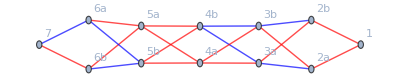

```mathematica
Graph[G,EdgeStyle->eLabels,ImageSize->Full]
```

## B_3

```mathematica
Relations = {{x:___,1,1,y:___}->{x,y},{x:___,2,2,y:___}->{x,y},{x:___,3,3,y:___}->{x,y},{x:___,3,1,y:___}->{x,1,3,y},{x:___,3,2,3,y:___}->{x,2,3,2,y},{x:___,2,1,2,1,y:___}->{x,1,2,1,2,y},
{x:___,3,2,1,3,y:___}->{x,2,3,2,1,y},
{x:___,3,2,1,2,3,2,y:___}->{x,2,3,2,1,2,3,y}};
GenerateNewElements[list_]:=DeleteDuplicates[Join[list,Flatten[{Join[#,{1}],Join[#,{2}],Join[#,{3}]}&/@list,1]//.Relations]]
B3list=FixedPoint[GenerateNewElements,{{}}]
```

{{},{1},{2},{3},{1,2},{1,3},{2,1},{2,3},{3,2},{1,2,1},{1,2,3},{1,3,2},{2,1,2},{2,1,3},{2,3,2},{3,2,1},{1,2,1,2},{1,2,1,3},{1,2,3,2},{1,3,2,1},{2,1,2,3},{2,1,3,2},{2,3,2,1},{3,2,1,2},{1,2,1,2,3},{1,2,1,3,2},{1,2,3,2,1},{1,3,2,1,2},{2,1,2,3,2},{2,1,3,2,1},{2,3,2,1,2},{3,2,1,2,3},{1,2,1,2,3,2},{1,2,1,3,2,1},{1,2,3,2,1,2},{1,3,2,1,2,3},{2,1,2,3,2,1},{2,1,3,2,1,2},{2,3,2,1,2,3},{1,2,1,2,3,2,1},{1,2,1,3,2,1,2},{1,2,3,2,1,2,3},{2,1,2,3,2,1,2},{2,1,3,2,1,2,3},{1,2,1,2,3,2,1,2},{1,2,1,3,2,1,2,3},{2,1,2,3,2,1,2,3},{1,2,1,2,3,2,1,2,3}}

```mathematica
ConjugateList[w_]:=Table[Join[w,{i},Reverse[w]]//.Relations,{i,1,3}]
T=DeleteDuplicates[Flatten[ConjugateList/@B3list,1]]
```

{{1},{2},{3},{1,2,1},{2,1,2},{2,3,2},{1,2,3,2,1},{3,2,1,2,3},{2,1,2,3,2,1,2}}

```mathematica
FindChildren[w_]:=Select[(Join[#,w]&/@T)//.Relations//DeleteDuplicates,Length[#]-1==Length[w]&]
ConvertToString[w_]:=If[Length[w]>0,StringJoin@@ToString/@w,"0"]
GetEdges[w_]:=((ConvertToString[w]->#&)@*ConvertToString)/@FindChildren[w]
edges = Flatten[GetEdges/@B3list]
```

{0→1,0→2,0→3,1→21,1→13,1→12,2→12,2→32,2→21,2→23,3→13,3→23,3→32,12→212,12→132,12→121,12→123,13→213,13→123,13→321,13→132,21→121,21→321,21→212,21→213,23→123,23→232,23→213,32→132,32→232,32→321,121→1212,121→1321,121→1213,123→2123,123→1232,123→1213,132→2132,132→1232,132→3212,132→1321,212→1212,212→3212,212→2132,212→2123,213→1213,213→2321,213→2123,213→2132,232→1232,232→2132,232→2321,321→1321,321→2321,321→3212,1212→13212,1212→21321,1212→12132,1212→12123,1213→12123,1213→12321,1213→12132,1232→21232,1232→12132,1232→32123,1232→12321,1321→21321,1321→12321,1321→13212,2123→12123,2123→32123,2123→21232,2132→12132,2132→23212,2132→21232,2132→21321,2321→12321,2321→21321,2321→32123,2321→23212,3212→13212,3212→23212,3212→32123,12123→132123,12123→212321,12123→121232,12132→121232,12132→123212,12132→121321,12321→212321,12321→121321,12321→132123,12321→123212,13212→213212,13212→123212,13212→132123,21232→121232,21232→232123,21232→212321,21321→121321,21321→213212,21321→212321,23212→123212,23212→213212,23212→232123,32123→132123,32123→232123,121232→1232123,121232→2123212,121232→1212321,121321→1212321,121321→1213212,123212→2123212,123212→1213212,123212→1232123,132123→2132123,132123→1232123,212321→1212321,212321→2132123,212321→2123212,213212→1213212,213212→2123212,213212→2132123,232123→1232123,232123→2132123,1212321→12132123,1212321→12123212,1213212→12123212,1213212→12132123,1232123→21232123,1232123→12132123,2123212→12123212,2123212→21232123,2132123→12132123,2132123→21232123,12123212→121232123,12132123→121232123,21232123→121232123}

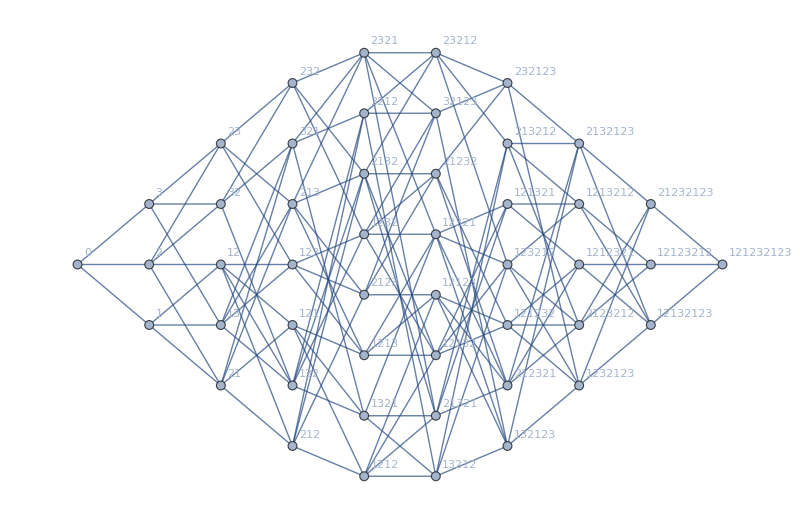

```mathematica
G=UndirectedGraph[edges,ImageSize->800,VertexLabels->"Name",GraphLayout->{"MultipartiteEmbedding", "VertexPartition"->{1,3,5,7,8,8,7,5,3,1}}]
```

```mathematica
nEdges = EdgeCount[G]
CycleAllowedQ[c_]:=(Length@DeleteDuplicates@(StringLength/@DeleteDuplicates[Flatten[Table[c[[j,k]],{j,1,4},{k,1,2}]]]))==3
cycles=Select[FindCycle[G,{4},All],CycleAllowedQ];
NormalFormEdge[e_]:=UndirectedEdge@@Sort[{e[[1]],e[[2]]}]
edgeAssoc = Association[#[[1]]->#[[2]]&/@Transpose[{NormalFormEdge/@EdgeList[G],Range[nEdges]}]];
edgeAssocInverse = Association[#[[1]]->#[[2]]&/@Transpose[{Range[nEdges],NormalFormEdge/@EdgeList[G]}]];
cycleNumbers=Sort/@Map[edgeAssoc@*NormalFormEdge,cycles,{2}];
BadCycles[signs_]:=Position[Times@@signs[[#]]&/@cycleNumbers,1]//Flatten
BadEdges[cycles_]:=cycleNumbers[[cycles]]//Flatten//DeleteDuplicates
```

138

{1,1,1,1,1,-1,-1,1,-1,1,1,-1,1,1,-1,1,-1,-1,1,-1,1,1,-1,-1,1,-1,1,-1,-1,1,-1,-1,-1,1,1,1,1,1,1,-1,-1,1,1,1,1,1,1,-1,-1,1,1,-1,-1,-1,-1,1,1,1,-1,-1,-1,1,1,-1,1,1,-1,1,-1,-1,1,-1,1,1,-1,1,1,1,-1,-1,1,1,-1,-1,1,1,1,-1,-1,1,-1,1,-1,1,1,-1,1,1,-1,1,1,1,1,1,1,1,1,1,1,1,-1,1,1,-1,1,1,-1,1,-1,1,1,-1,1,-1,-1,-1,1,1,1,1,1,1,1,1,-1,1,-1,1}

32

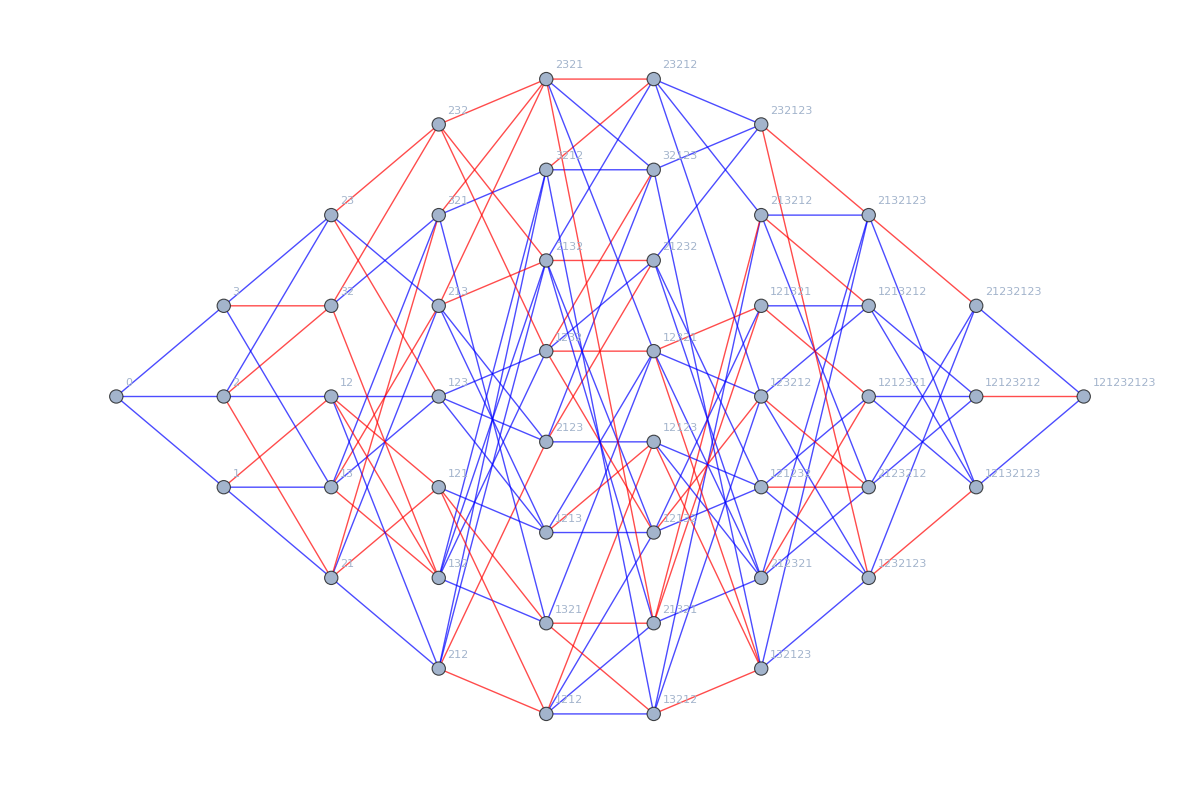

```mathematica
signs=RandomChoice[{-1,1},nEdges];
signs=ConstantArray[1,nEdges];
badCycles = BadCycles[signs];
l=Length[badCycles];
lmin=l;
While[lmin>0,
choice= RandomChoice[BadEdges[badCycles]];
signs[[choice]]=-1*signs[[choice]];
badCycles=BadCycles[signs];
lprime = Length[badCycles];
If[lprime>l,
signs[[choice]]=-1*signs[[choice]];,
l=lprime;x=l;
];
If[l<lmin,lmin=l];
]
signs
Total[signs]
eLabels = #[[1]]->#[[2]]&/@({edgeAssocInverse/@Range[nEdges],<|1->Blue,-1->Red|>/@signs}//Transpose);
UndirectedGraph[edges,VertexLabels->"Name",ImageSize->1200,EdgeStyle->eLabels,GraphLayout->{"MultipartiteEmbedding", "VertexPartition"->{1,3,5,7,8,8,7,5,3,1}}]
```

## S_n

```mathematica
Remove["Global`*"]
```

We compute the sign distribution for the BGG complex of S_n for arbitrary n (although it becomes infeasible for n>7). First we build the graph, its vertices are elements of the Weyl group W=S_n. Recall that W is generated  by s_1,... s_(n-1) where s_i=(i,i+1), that is every element of W is a word in the s_i, and hence every element of W also has a ‘length’ given by the length of the shortest word in s_i presenting it. We enumerate all the elements of W and then in order to compute products we ask Mathematica to convert these elements to built-in permutation cycles.
Define T = ⟨(i,j) | i<j⟩, then we have an edge w→tw (with w∈W, t∈T) if the length of tw is exactly one bigger than that of w. We can now easily build the graph.

Now we want to assign a sign to all the edges of the graph such that the product of signs for each admissible cycle is -1. A cycle in this graph is admissible if it is of length 4, and its vertices are words of length  l→l+1→l+2→l+1. This just excludes the hourglass-shaped cycles of form l→l+1→l→l+1.

```mathematica
n=4; (*set n*)
t[i_,j_]:=Block[{},
Assert[1≤ i≤ j≤ n];
Table[k,{k,j-1,i,-1}]
]
indices=Table[{a[i],i},{i,n}];
Sn = Flatten[Table[Join@@(t@@@indices),##],n-1]&@@indices; (*Enumerate all the elements of Subscript[S, n] using the approach outlined in some Stackexchange post. all these words are of minimum length, but this presentation is certainly not unique. *)
```

```mathematica
s[i_]:=Cycles[{{i,i+1}}]
stringToCycle = Association[StringJoin@(ToString/@#)->PermutationProduct@@(s/@#)&/@Sn];(*given a word, e.g. 12131, convert it to a permutation*)
cycleToString =Association[PermutationProduct@@(s/@#)-> StringJoin@(ToString/@#)&/@Sn];StringProduct[x__]:=cycleToString[PermutationProduct@@(stringToCycle/@{x})] (*given a permutation, convert it to a word in the Subscript[s, i], in particular in the form we used in our enumeration of Subscript[s, n]*)
T=SortBy[cycleToString/@Flatten[Table[Cycles[{{i,j}}],{i,1,n-1},{j,i+1,n}]],StringLength];
Sns =SortBy[StringJoin/@Map[ToString,Sn,{2}],StringLength];
```

```mathematica
edges = Select[#[[1]]->StringProduct[#[[2]],#[[1]]]&/@Tuples[{Sns,T}],StringLength[#[[1]]]==StringLength[#[[2]]]-1&]; (*find all the edges w->tw*)
partition= Last/@Tally[StringLength/@Sns];(*The graph is naturally multipartite with each part corresponding to a word length. We compute the size of each part, this makes the displayed graph more pretty*)
G=UndirectedGraph[edges,GraphLayout->{"MultipartiteEmbedding", "VertexPartition"->partition},VertexLabels->"Name",ImageSize->1200];
```

```mathematica
nEdges = EdgeCount[G]
CycleAllowedQ[c_]:=(Length@DeleteDuplicates@(StringLength/@DeleteDuplicates[Flatten[Table[c[[j,k]],{j,1,4},{k,1,2}]]]))==3 (*A cycle is allowed iff it contains precisely three different word lengths*)
cycles=Select[FindCycle[G,{4},All],CycleAllowedQ];(*Find all the cycles of length 4 in the graph, and then select only the admissible cycles. For large graphs this can take a while*)
NormalFormEdge[e_]:=UndirectedEdge@@Sort[{e[[1]],e[[2]]}](*function to have vertices of an edge sorted*)
edgeAssoc = Association[#[[1]]->#[[2]]&/@Transpose[{NormalFormEdge/@EdgeList[G],Range[nEdges]}]];(*assign a number to all the edges*)
edgeAssocInverse = Association[#[[1]]->#[[2]]&/@Transpose[{Range[nEdges],NormalFormEdge/@EdgeList[G]}]]; (*convert edge number back into the edge*)
cycleNumbers=Sort/@Map[edgeAssoc@*NormalFormEdge,cycles,{2}]; (*list of cycles by edge numbers*)
BadCycles[signs_]:=Position[Map[Times@@signs[[#]]&,cycleNumbers],1]//Flatten (*for all cycles compute the product of their signs, pick out the cycles for which this product is 1*)
BadEdges[cycles_]:=cycleNumbers[[cycles]]//Flatten//DeleteDuplicates (*given a list of cycles find the set of unique edges in it*)
BadCyleCount[signs_]:= Count[Map[Times@@signs[[#]]&,cycleNumbers],1] (*Count the number of bad cycles*)
ComputeBadCycleCount[choice_]:=(BadCyleCount@*ReplacePart)[signs,choice->signs[[choice]]*-1] (*compute the amount of bad cycles if we were to change the sign of a particular edge*)
```

58

```mathematica
cycleAssoc=Quotient[#,4,1]+1&/@PositionIndex[Flatten[cycleNumbers]];(*For each edge find the cycles in which it is contained*)
```

```mathematica
checkChoice[choice_]:=Module[{cycles},
cycles=cycleNumbers[[cycleAssoc[choice]]];
Return[Total[Map[Times@@signs[[#]]&,cycles]]>0]
] (*check whether flipping the sign of an edge would reduce the number of bad cycles. For each cycle the edge is contained in, compute the product of signs and sum the result. If this sum is larger than zero, then there is a larger number of cycles containing the edge which has product 1 than -1, and therefore flipping the sign is beneficial. Otherwise it is not*)
```

```mathematica
signs=RandomChoice[{-1,1},nEdges];(*initiallize the signs by just picking random signs for each edge*)
badEdges=(RandomSample@*BadEdges@*BadCycles)[signs]; (*find all the bad edges and randomize the order, so we can just sample from it*)
l=BadCyleCount[signs];
lmin=l;
lshow=l;
beshow=Length[badEdges];
Dynamic[lshow]  (*dynamically show the number of bad cycles and bad edges*)
Dynamic[beshow]
numRandomiziation=1;
While[l>0,
computation=SelectFirst[badEdges,checkChoice];(*Find the first edge which would be beneficial to flip*)
If[MissingQ[computation], (*if we didn't find any edges to flip, we flip some number of edges. Every time we fail we flip twice as many edges until we have improvement over the previous best situation and we reset the number to 1*)
Do[
choice=RandomChoice[Keys[edgeAssocInverse]];
signs[[choice]]=-1*signs[[choice]];,numRandomiziation
];numRandomiziation*=2;,
signs[[computation]]=signs[[computation]]*(-1)(*if we found an edge to flip, flip it*)

];
lnew = BadCyleCount[signs];
If[lnew<l,l=lnew;numRandomiziation=1;lshow=l;,
];
badEdges=(RandomSample@*BadEdges@*BadCycles)[signs];beshow=Length[badEdges];(*compute the number of bad edges*)

];
signs;
Total[signs](*total of the signs, so we can see if there are more positive than negative signs*)
eLabels = #[[1]]->#[[2]]&/@({edgeAssocInverse/@Range[nEdges],<|1->Blue,-1->Red|>/@signs}//Transpose);(*display the graph with positive edges labelled blue, negative red*)
```

4

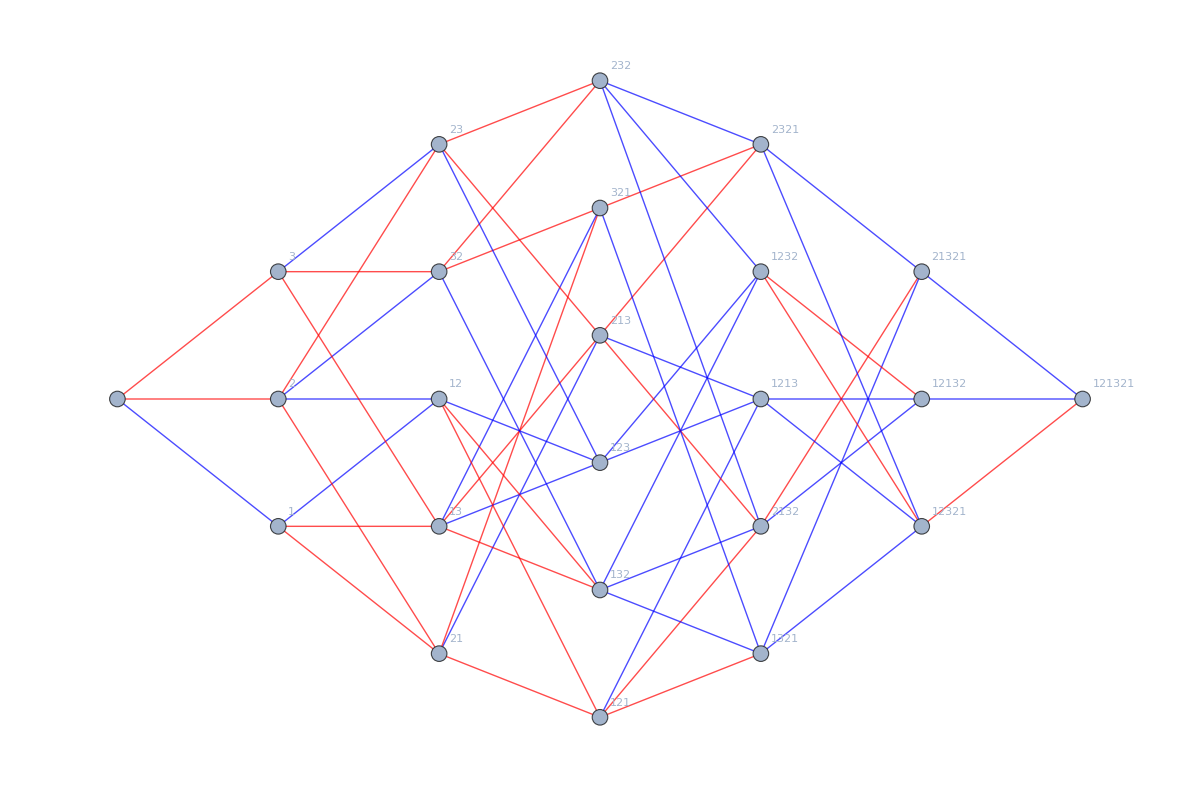

```mathematica
UndirectedGraph[edges,ImageSize->1200,EdgeStyle->eLabels,GraphLayout->{"MultipartiteEmbedding", "VertexPartition"->partition},VertexLabels->"Name"]
```